```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.2+2.3/2_2_by_Marina.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.2+2.3/2.2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.2+2.3/~$2_2_by_Marina.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/2.2+2.3/2_2_by_Marina.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1 = makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
data1 =raw⟦3⟧⟦2;;⟧
```

{{2596.,7032.},{2564.,6929.},{2504.,6717.},{2490.,6678.},{2461.,6599.},{2434.,6533.},{2426.,6507.},{2388.,6402.},{2380.,6383.},{2364.,6334.},{2354.,6305.},{2336.,6267.},{2314.,6217.},{2292.,6164.},{2282.,6143.},{2264.,6096.},{2254.,6074.},{2232.,6030.},{2210.,5976.},{2196.,5945.},{2166.,5882.},{2152.,5852.},{1883.,5401.},{1841.,5341.},{1834.,5331.}}

```mathematica
dataset2 = makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
data2 =raw⟦4⟧⟦2;;⟧
```

{{2562.,6907.},{2320.,6234.},{2115.,5792.},{2104.,5770.},{1923.,5461.},{1494.,4916.},{821.,4358.},{265.,4047.}}

```mathematica
data = Union[data1,data2]
```

{{265.,4047.},{821.,4358.},{1494.,4916.},{1834.,5331.},{1841.,5341.},{1883.,5401.},{1923.,5461.},{2104.,5770.},{2115.,5792.},{2152.,5852.},{2166.,5882.},{2196.,5945.},{2210.,5976.},{2232.,6030.},{2254.,6074.},{2264.,6096.},{2282.,6143.},{2292.,6164.},{2314.,6217.},{2320.,6234.},{2336.,6267.},{2354.,6305.},{2364.,6334.},{2380.,6383.},{2388.,6402.},{2426.,6507.},{2434.,6533.},{2461.,6599.},{2490.,6678.},{2504.,6717.},{2562.,6907.},{2564.,6929.},{2596.,7032.}}

```mathematica
nlm = NonlinearModelFit[data,λ0+B/(θ-θ0),{λ0,B,θ0},θ]
```

FittedModel[2338.16-(6.28525×10^6)/(-3935.8+θ)]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

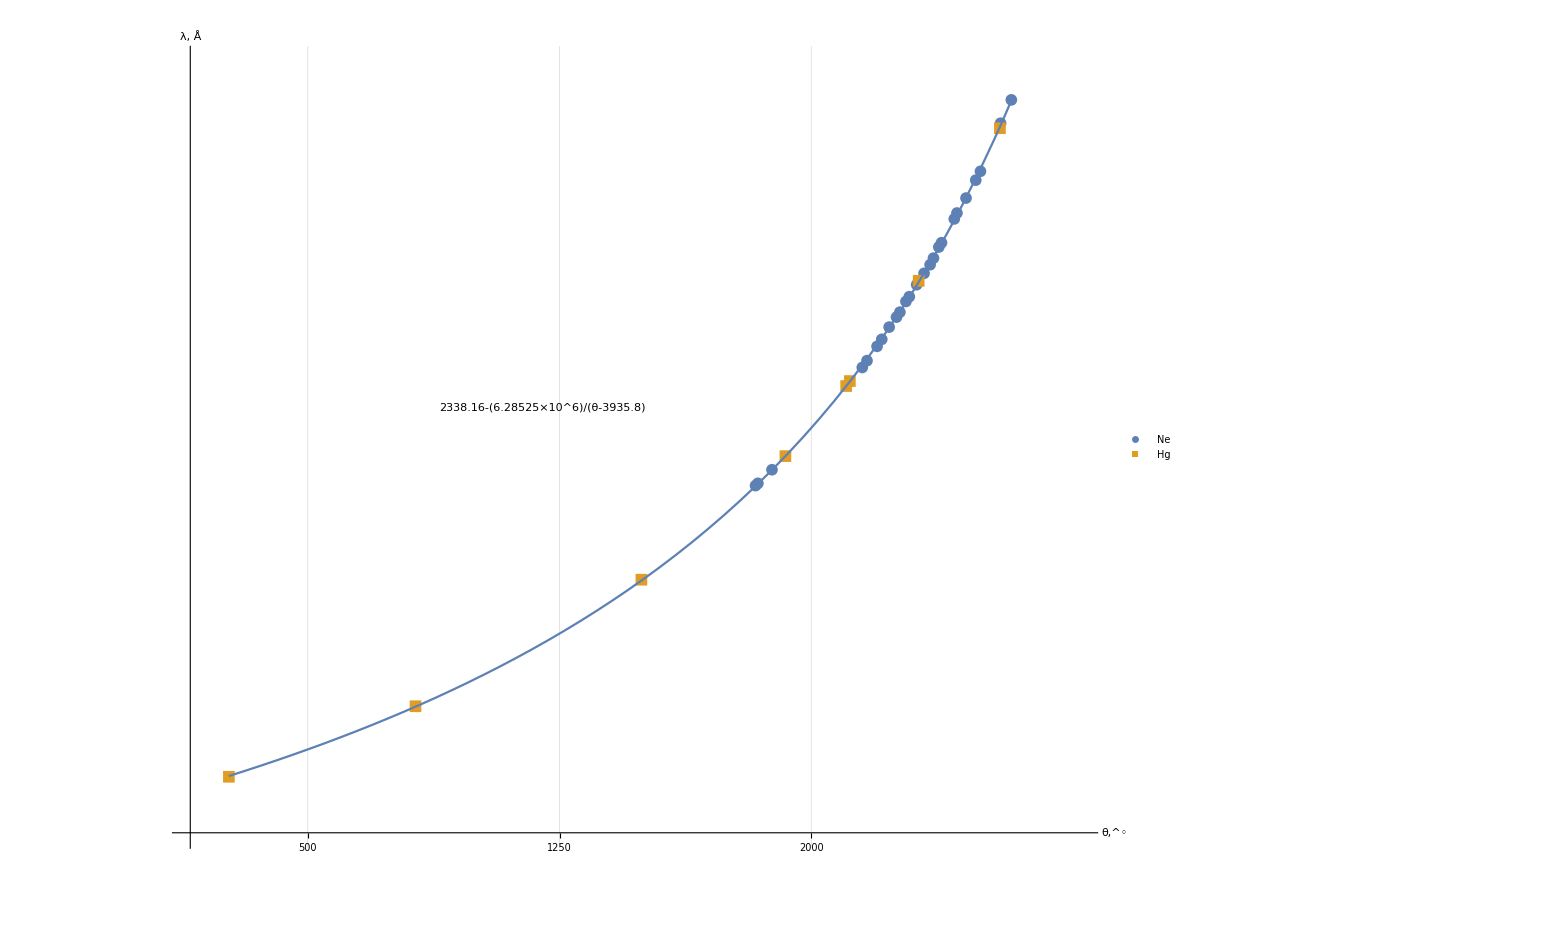

```mathematica
Show[
ListPlot[
{dataset1,dataset2},
PlotRange-> {{150,2800},{3800,7200}},
Ticks-> {Range[-10000,10000, 250],Range[-10000,10000, 250]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["θ,^◦", Large], Style["λ, Å", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-10000,10000, 50],Range[-10000,10000, 100]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{"Ne","Hg"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.8]}
]
],
(*Plot[Callout[nlm[x],Normal[nlm],{1100,5450},Frame->True,RoundingRadius->10,FrameMargins->30,Appearance->None,LabelStyle->{18,Black},Background->GrayLevel[1],"CalloutStyle"->Black],{x,265,2596}],*)
Plot[nlm[x],{x,265,2596}],
Graphics[{(*EdgeForm[Black],White,Rectangle[Scaled[{0.32,0.5}],Scaled[{0.48,0.6}],RoundingRadius->0.3],*)Black,Inset[Framed[Style[Normal[nlm],18],RoundingRadius->10,Background->White],Scaled[{0.4,0.55}]]}]
]
```

```mathematica
Symbol
```

Symbol

```mathematica
Normal@nlm
```

2338.16-(6.28525×10^6)/(-3935.8+θ)

```mathematica
Plot[Callout[nlm[x],Normal[nlm],{1000,5750}],{x,265,2596}]
```

-Graphics-



```mathematica
Graphics[Rectangle[RoundingRadius->0.3]]
```

```mathematica
Graphics[{EdgeForm[Black],White,Rectangle[Scaled[{0.32,0.5}],Scaled[{0.48,0.6}]],Black,Inset[Style[Normal[nlm],18],Scaled[{0.4,0.55}]]}]
```

-Graphics-

## Dataset 3

```mathematica
dataset3 = makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs = dataset3[All, <|"n"-> (#n&), "l" -> (Around[#l,#dl] &)|>]
```

Dataset[<>]

```mathematica
dataline = raw⟦5⟧⟦2;;⟧⟦All,1;;2⟧
```

{{0.139,1.522},{0.188,2.049},{0.21,2.289},{0.222,2.425}}

```mathematica
line1 = LinearModelFit[dataline,{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+10.914 x]

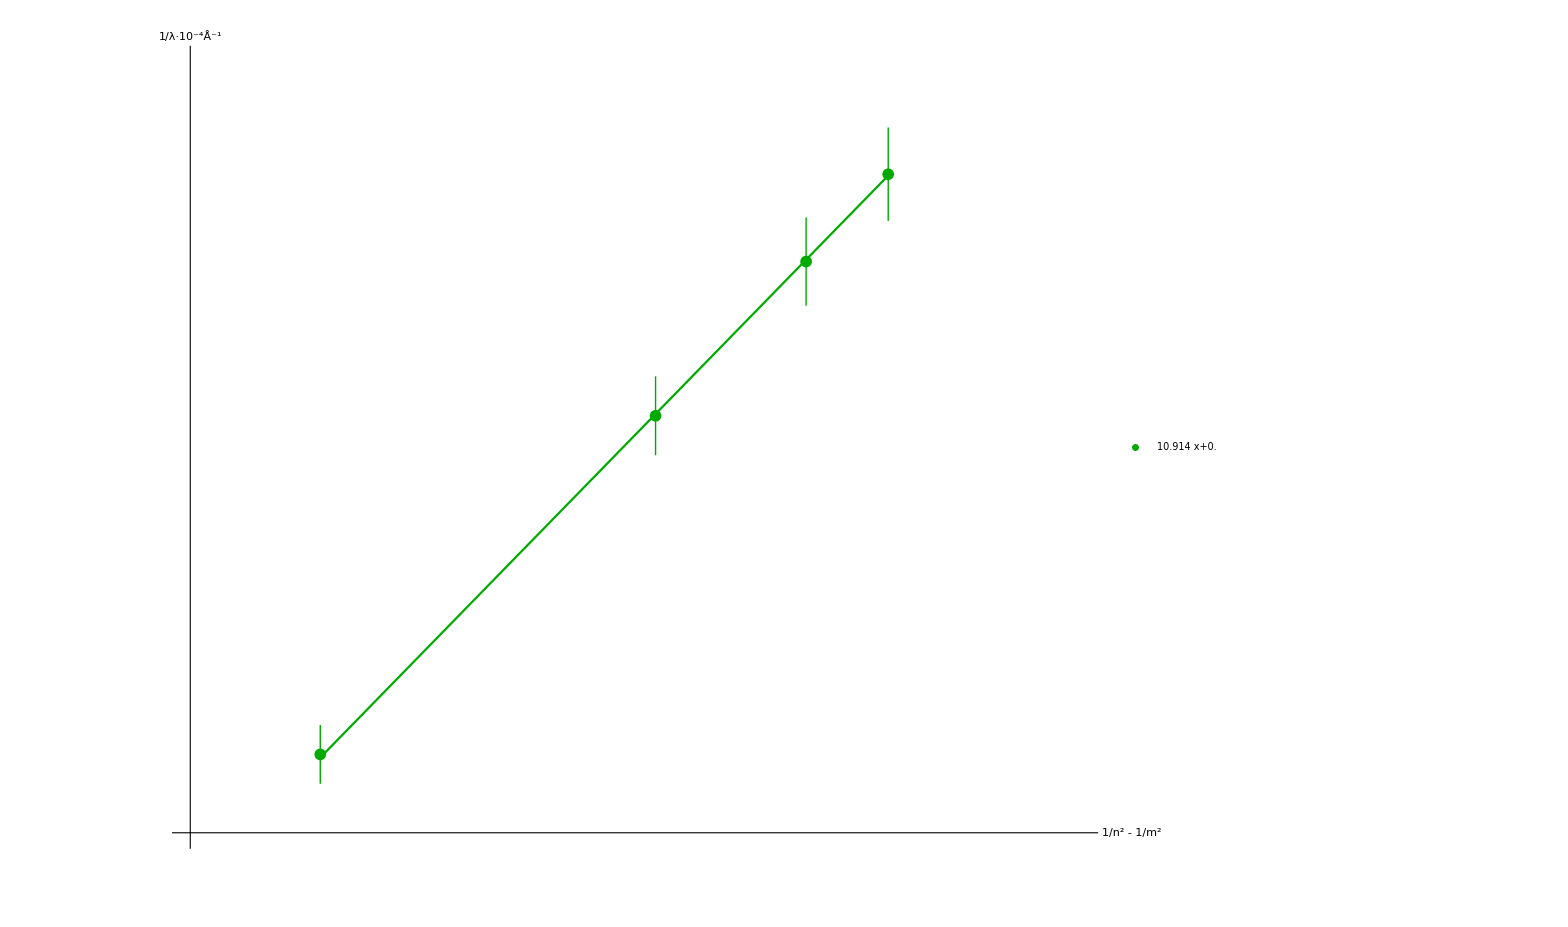

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
PlotRange-> {{0.12,0.25},{1.4,2.6}},
Ticks-> {Range[-1000,1000, 0.01],Range[-1000,1000, 0.1]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["1/n^2 - 1/m^2", Large], Style["1/λ·10^-4Å^-1", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.005],Range[-1000,1000, 0.05]},
LabelStyle->Black,
PlotStyle->Darker@Green,
PlotLegends->Placed[LineLegend[
{Normal@line1},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[line1[x],{x,0.139,0.222},PlotStyle->Darker[Green]]
]
```

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 10.914 | 0.0124074 | 879.639 | 1.29238×10^-6